### checking one file, and determining approximate pixel size

```mathematica
aDatasetQQ=Import[ToString["E:\\ScanDataFiles\\NASAcylindricalWavefrontInterferometer\\20240214-HighRi-P2-Sample2-ROC77mm-Mask25mm-Pitched\\20240214-1617-HighRi-P2-Sample2-ROC77mm-Mask25mm-1Fringe.h5"],{"HDF5","Data",3(* third [second] dataset in the HDF5 file *)}];
```

#### chedking the size of the sample (25 mm Y)

```mathematica
maskXstartSample = 690;
maskXendSample = 950;
maskYstartSample = 740;
maskYendSample= 985

Image[
normalizeAmplitudeOf2Darray[
maskImageDataToPoints[
aDatasetQQ,
(* maskXstart_ *)maskXstartSample ,
(* maskXend_ *)maskXendSample,
(* maskYstart_ *)maskYstartSample,
(* maskYend_ *)maskYendSample
]
]
]
```

985

-Graphics-

#### estimating vertical pixels size

```mathematica
pixSizeY=(25/(maskYendSample-maskYstartSample))*10^6//N
```

102041.

### Converting the files to Zygo *. xyz

#### checking the *. h5 files in a directory

```mathematica
sampleFiles=FileNames["E:\\ScanDataFiles\\NASAcylindricalWavefrontInterferometer\\20240214-HighRi-P2-Sample2-ROC77mm-Mask25mm-Pitched\\*.h5"]
```

{E:\ScanDataFiles\NASAcylindricalWavefrontInterferometer\20240214-HighRi-P2-Sample2-ROC77mm-Mask25mm-Pitched\20240214-1617-HighRi-P2-Sample2-ROC77mm-Mask25mm-1Fringe.h5,E:\ScanDataFiles\NASAcylindricalWavefrontInterferometer\20240214-HighRi-P2-Sample2-ROC77mm-Mask25mm-Pitched\20240214-1619-HighRi-P2-Sample2-ROC77mm-Mask25mm-2Fringes.h5,E:\ScanDataFiles\NASAcylindricalWavefrontInterferometer\20240214-HighRi-P2-Sample2-ROC77mm-Mask25mm-Pitched\20240214-1621-HighRi-P2-Sample2-ROC77mm-Mask25mm-3Fringes.h5,E:\ScanDataFiles\NASAcylindricalWavefrontInterferometer\20240214-HighRi-P2-Sample2-ROC77mm-Mask25mm-Pitched\20240214-1622-HighRi-P2-Sample2-ROC77mm-Mask25mm-4Fringes.h5,E:\ScanDataFiles\NASAcylindricalWavefrontInterferometer\20240214-HighRi-P2-Sample2-ROC77mm-Mask25mm-Pitched\20240214-1624-HighRi-P2-Sample2-ROC77mm-Mask25mm-5Fringes.h5}

#### converting to Zygo *. xyz

```mathematica
Table[
convertNASAcylindricalDataToZygoXYZ[
(* fileName_ *)sampleFiles[[nn]],
(* maskXstart_ *)maskXstartSample,
(* maskXend_ *)maskXendSample ,
(* maskYstart_ *)maskYstartSample,
(* maskYend_ *)maskYendSample,
(* pixelSizeInNanometers_ *)pixSizeY
],
{nn,1,Length[sampleFiles]}]
```

{E:\ScanDataFiles\NASAcylindricalWavefrontInterferometer\20240214-HighRi-P2-Sample2-ROC77mm-Mask25mm-Pitched\20240214-1617-HighRi-P2-Sample2-ROC77mm-Mask25mm-1Fringe.xyz,E:\ScanDataFiles\NASAcylindricalWavefrontInterferometer\20240214-HighRi-P2-Sample2-ROC77mm-Mask25mm-Pitched\20240214-1619-HighRi-P2-Sample2-ROC77mm-Mask25mm-2Fringes.xyz,E:\ScanDataFiles\NASAcylindricalWavefrontInterferometer\20240214-HighRi-P2-Sample2-ROC77mm-Mask25mm-Pitched\20240214-1621-HighRi-P2-Sample2-ROC77mm-Mask25mm-3Fringes.xyz,E:\ScanDataFiles\NASAcylindricalWavefrontInterferometer\20240214-HighRi-P2-Sample2-ROC77mm-Mask25mm-Pitched\20240214-1622-HighRi-P2-Sample2-ROC77mm-Mask25mm-4Fringes.xyz,E:\ScanDataFiles\NASAcylindricalWavefrontInterferometer\20240214-HighRi-P2-Sample2-ROC77mm-Mask25mm-Pitched\20240214-1624-HighRi-P2-Sample2-ROC77mm-Mask25mm-5Fringes.xyz}

### quick look at image data of the files

```mathematica
quickLook=Table[
quickLookAtImageData[
maskImageDataToPoints[
wavelengthCylindricalInterferometer*Import[ToString[fileName],{"HDF5","Data",3(* third [second] dataset in the HDF5 file *)}],
(* maskXstart_ *)maskXstartSample,
(* maskXend_ *)maskXendSample ,
(* maskYstart_ *)maskYstartSample,
(* maskYend_ *)maskYendSample
]
]//MatrixForm,
{fileName,sampleFiles}];
```

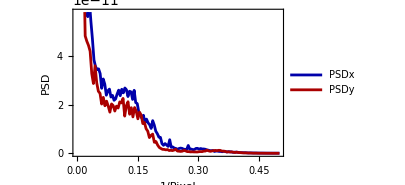
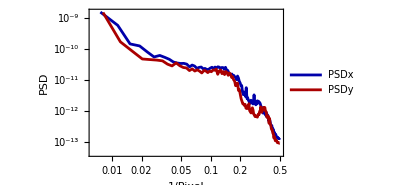
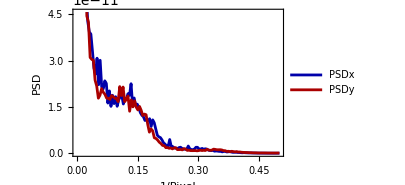
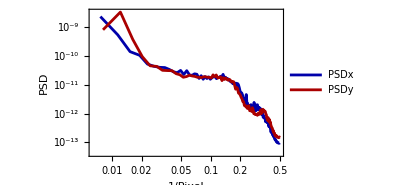
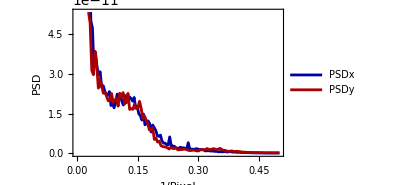
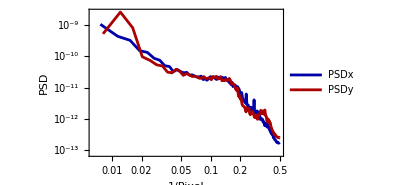
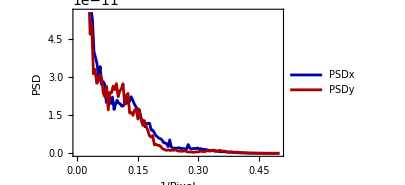
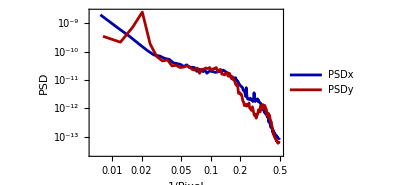
{(RMS :   
0.0000661107
Peak to Valley : 
0.000621152
{ Min ,  Max } :
{0.000051982,0.000673134}
{ numXcoords , numYcoords }  : 
{261,246}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
0.0000657348
-Graphics-
-Graphics-),(RMS :   
0.0000741377
Peak to Valley : 
0.000609966
{ Min ,  Max } :
{0.000063168,0.000673134}
{ numXcoords , numYcoords }  : 
{261,246}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
0.0000737351
-Graphics-
-Graphics-),(RMS :   
0.0000745365
Peak to Valley : 
0.000603386
{ Min ,  Max } :
{0.000069748,0.000673134}
{ numXcoords , numYcoords }  : 
{261,246}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
0.0000729604
-Graphics-
-Graphics-),(RMS :   
0.0000712605
Peak to Valley : 
0.000613256
{ Min ,  Max } :
{0.000059878,0.000673134}
{ numXcoords , numYcoords }  : 
{261,246}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
0.0000711281
-Graphics-
-Graphics-),(RMS :   
0.0000769765
Peak to Valley : 
0.000616546
{ Min ,  Max } :
{0.000056588,0.000673134}
{ numXcoords , numYcoords }  : 
{261,246}
Data : 0 to 1 GrayScale  : 
-Graphics-
Normalized Data  : 
-Graphics-
Plane Detrended  : 
-Graphics-
resid rms: 
0.0000769641
-Graphics-
-Graphics-)}

```mathematica
quickLook
```